# “Semi-Inclusive Deep Inelastic Scattering in Wandzura-Wilczek-type approximation” S. Bastami, H. Avakian, A. V. Efremov, A. Kotzinian, B. U. Musch, B. Parsamyan, A. Prokudin, M. Schlegel, G. Schnell, P. Schweitzer, K. Tezgin, W. Vogelsang author : Alexei Prokudin, Kemal Tezgin email : prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/WW-SIDIS

```mathematica
<<wwsidis.m
```

Package WW-SIDIS contains the set of TMDs calculated with WW approximation and SIDIS structure functions

Copyright: Alexei Prokudin (PSU Berks), Kemal Tezgin (UConn), Version 1 (05/21/2018)

e-mail: prokudin@jlab.org

https://github.com/prokudin/WW-SIDIS

___________________________________________________________________________

Contains the following functions:

f1u[x_,Q2_ ] is the unpolarised collinear PDF for u quark

f1d[x_,Q2_ ] is the unpolarised collinear PDF for d quark

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from Grids/mstw2008lo.00.dat

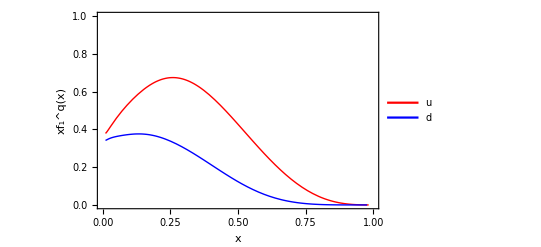

```mathematica
Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```